```mathematica
arrow[i_,j_]:={Which[DD[[i,j]]==1,Line[{{i-.9,j-.6},{i-.65,j-.35},{i-.8,j-.2},{i-.2,j-.2},{i-.2,j-.8},{i-.35,j-.65},{i-.6,j-.9},{i-.9,j-.6}}],
DD[[i,j]]==2,Line[{{i-.7,j-.9},{i-.7,j-.5},{i-.9,j-.5},{i-.5,j-.1},{i-.1,j-.5},{i-.3,j-.5},{i-.3,j-.9},{i-.7,j-.9}}],
DD[[i,j]]==3,Line[{{i-.1,j-.6},{i-.35,j-.35},{i-.2,j-.2},{i-.8,j-.2},{i-.8,j-.8},{i-.65,j-.65},{i-.4,j-.9},{i-.1,j-.6}}],
DD[[i,j]]==4,Line[{{i-.1,j-.7},{i-.5,j-.7},{i-.5,j-.9},{i-.9,j-.5},{i-.5,j-.1},{i-.5,j-.3},{i-.1,j-.3},{i-.1,j-.7}}],
DD[[i,j]]==5,Line[{{i-.1,j-.4},{i-.35,j-.65},{i-.2,j-.8},{i-.8,j-.8},{i-.8,j-.2},{i-.65,j-.35},{i-.4,j-.1},{i-.1,j-.4}}],
DD[[i,j]]==6,Line[{{i-.7,j-.1},{i-.7,j-.5},{i-.9,j-.5},{i-.5,j-.9},{i-.1,j-.5},{i-.3,j-.5},{i-.3,j-.1},{i-.7,j-.1}}],
DD[[i,j]]==7,Line[{{i-.9,j-.4},{i-.65,j-.65},{i-.8,j-.8},{i-.2,j-.8},{i-.2,j-.2},{i-.35,j-.35},{i-.6,j-.1},{i-.9,j-.4}}],
DD[[i,j]]==8,Line[{{i-.9,j-.7},{i-.5,j-.7},{i-.5,j-.9},{i-.1,j-.5},{i-.5,j-.1},{i-.5,j-.3},{i-.9,j-.3},{i-.9,j-.7}}]]
}
```

```mathematica
initialize:=(DD=Table[Which[
i==(width+1)/2&&j==(depth+1)/2,Random[Integer,{1,8}],
i<(width+1)/2&&j==(depth+1)/2,Mod[Random[Integer,{5,9}],8]+1,
i>(width+1)/2&&j==(depth+1)/2,Random[Integer,{2,6}],
i==(width+1)/2&&j<(depth+1)/2,Mod[Random[Integer,{7,11}],8]+1,
i==(width+1)/2&&j>(depth+1)/2,Random[Integer,{4,8}],
i≤width/2&&j≤depth/2,Mod[Random[Integer,{7,9}],8]+1,
i≤width/2,Random[Integer,{6,8}],
j≤depth/2,Random[Integer,{2,4}],
True,Random[Integer,{4,6}]],{i,1,width},{j,1,depth}];)
```

```mathematica
pointedat[i_,j_]:=Which[
DD[[i,j]]==2,Table[{i,k},{k,j+1,depth}],
DD[[i,j]]==6,Table[{i,k},{k,1,j-1}],
DD[[i,j]]==4,Table[{k,j},{k,1,i-1}],
DD[[i,j]]==8,Table[{k,j},{k,i+1,width}],
DD[[i,j]]==1,Table[{i+k,j+k},{k,1,Min[width-i,depth-j]}],
DD[[i,j]]==7,Table[{i+k,j-k},{k,1,Min[width-i,j-1]}],
DD[[i,j]]==5,Table[{i-k,j-k},{k,1,Min[i-1,j-1]}],
DD[[i,j]]==3,Table[{i-k,j+k},{k,1,Min[i-1,depth-j]}]]
```

```mathematica
exactly2[v_]:=BooleanCountingFunction[{2},Length[v]]@@v
```

```mathematica
pic:=Module[{},
Print[Style[Show[Graphics[{
Line[{{-.1,-.1},{-.1,depth+.1},{width+.1,depth+.1},{width+.1,-.1},{-.1,-.1}}],
Table[arrow[i,j],{i,1,width},{j,1,depth}]
}],AspectRatio->Automatic,ImageSize->40 (width+.2),PlotRange->{{-.11,width+.11},{-.11,depth+.11}}],Antialiasing->False]];
Print[Style[Show[Graphics[{Line[{{-.1,-.1},{-.1,depth+.1},{width+.1,depth+.1},{width+.1,-.1},{-.1,-.1}}],
Table[If[solns[[i,j]]==1,{arrow[i,j]},{}],{i,1,width},{j,1,depth}]
}],AspectRatio->Automatic,ImageSize->40 (width+.2),PlotRange->{{-.11,width+.11},{-.11,depth+.11}}],Antialiasing->False]];]
```

```mathematica
While[0==0,
width=6;
depth=6;
initialize;
solns=SatisfiabilityInstances[Apply[And,Flatten[Table[Implies[x[i,j],exactly2[Map[x[Apply[Sequence,#]]&,pointedat[i,j]]]],{i,1,width},{j,1,depth}],1]],Flatten[Table[x[i,j],{i,1,width},{j,1,depth}],1],3];
If[Length[solns]==2,
solns=Partition[Complement[solns,{Table[False,{width depth}]}][[1]]/.{True->1,False->0},depth];pic;
]]
```

## 5x5

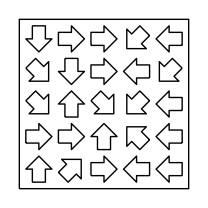

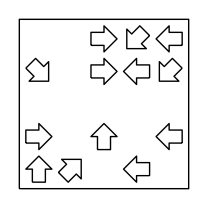

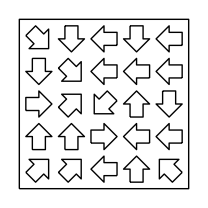

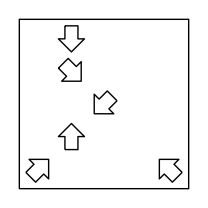

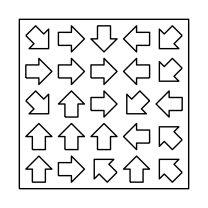

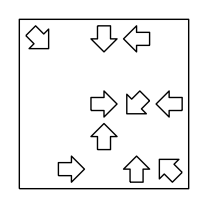

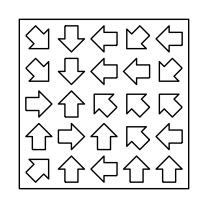

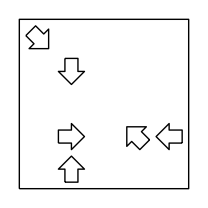

## 6x5

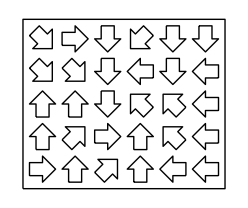

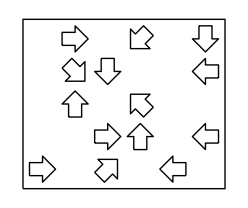

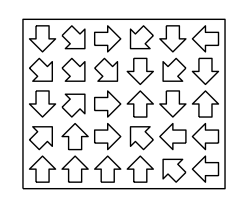

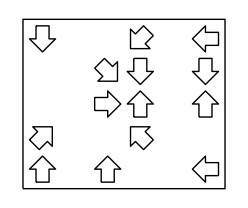

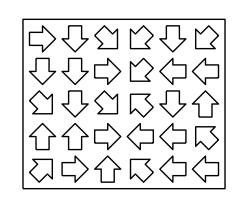

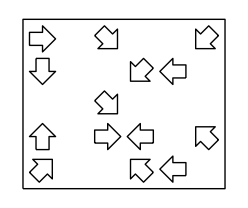

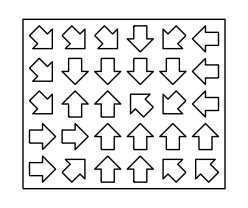

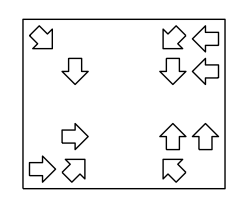

## 6x6